```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/code"];
```

## Problem 1

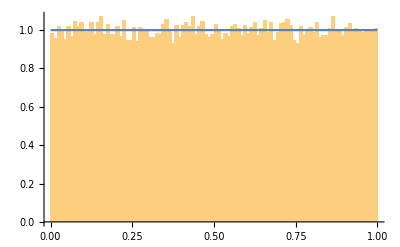

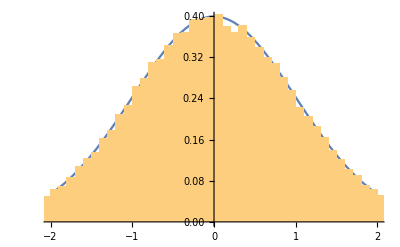

```mathematica
data = ReadList["!./p1 100000", {Number, Number}];
drand48 = Histogram[data[[All,1]], 100, PDF];
gausrand48 = Histogram[data[[All,2]], 100, PDF];
gaus = Plot[PDF[NormalDistribution[0,1],x],{x,-2,2}];
rand = Plot[1, {x, 0, 1}];
Show[drand48, rand]
Show[gaus, gausrand48]
```

## Problem 2

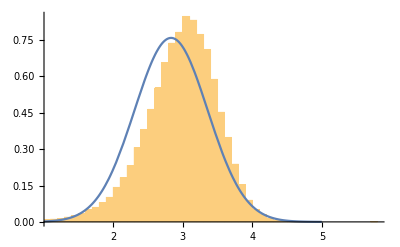

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/class"];
data = ReadList["!./a.out 1 2 4 1 100000"];
naive= Plot[PDF[NormalDistribution[Log[17],0.526],x],{x,0, 5}];
soph = Histogram[data,100, "PDF"];
Show[soph, naive]
```

## Problem 3

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/code"];
```

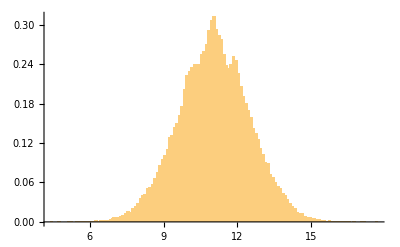

11.0474

1.43296

```mathematica
data = ReadList["!./p3 cannonball.dat 100000"];
g = data*-2;
Histogram[g, 100, PDF]
Mean[g]
StandardDeviation[g]
```

## Problem 4

Task 1:

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/code"];
data = ReadList["bootstrap.dat", {Number, Number}];
yi = Partition[data[[2;;,2]], 13];
Table[Mean[yi[[All, time]]], {time, 1,13}]
Table[StandardDeviation[yi[[All, time]]], {time, 1,13}]
```

{16381.3,16380.9,16377.6,16371.3,16364.3,16352.6,16340.3,16324.6,16306.,16286.1,16263.,16237.9,16210.1}

{101.903,101.563,102.517,101.983,101.296,103.33,102.216,102.911,101.821,102.012,101.756,101.967,102.882}

Task 2

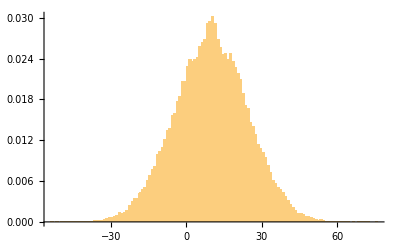

9.86106

14.4718

```mathematica
data = ReadList["!./p3 p4t2.dat 100000"];
g = data*-2;
Histogram[g, 100, PDF]
Mean[g]
StandardDeviation[g]
```

Task 3